# Optimal Boundary Value Problem Solver

## Wolfram 语言的使用规则

1. 所有内置函数的首字母大写
2. 函数参数在方括号[]中
3. 列表（范围或域）在花括号{}中
4. Shift-Enter进行计算

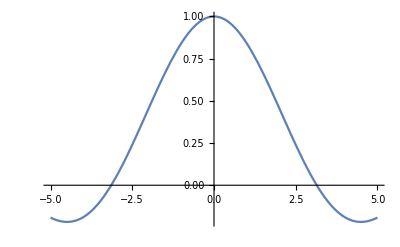

```mathematica
Plot[Sin[x]/x,{x, -5, 5}]
```

## 建议栏

```mathematica
x^2-10
```

-10+x^2

```mathematica
NSolve[Roots[Factor[∫(x^2-10)ⅆx]==0,x],{x}]
```

{{x→0.},{x→5.47723},{x→-5.47723}}

## 复合表达式

```mathematica
h = 20+17-5
2^h+3^h
```

32

1853024483819137

```mathematica
j=20+18-12; 2^j+3^j
```

2541932937193

## 定义函数

```mathematica
f[x_]:=x^2
```

```mathematica
f[3]
```

9

```mathematica
f[pi]
```

pi^2

```mathematica
f[{1,2,3,4}]
```

{1,4,9,16}

```mathematica
g[x_,y_]:=x^y
```

```mathematica
g[a,2]
```

a^2

## Solver

```mathematica
P0 = {{Pix}, {Piy}, {Piz}};
```

```mathematica
V0 = {{Vix}, {Viy}, {Viz}};
```

```mathematica
Pf = {{Pfx}, {Pfy}, {Pfz}}; Vf = {{0}, {0}, {0}};
```

```mathematica
delta = Flatten[{Pf-T*V0-P0, Vf-V0}]
```

{Pfx-Pix-T Vix,Pfy-Piy-T Viy,Pfz-Piz-T Viz,-Vix,-Viy,-Viz}

```mathematica
mat1 = {{-12/T^3, 0, 0, 6/T^2, 0, 0},{ 0, -12/T^3, 0, 0, 6/T^2, 0},{ 0,  0,-12/T^3, 0, 0, 6/T^2},{6/T^2, 0, 0, -2/T, 0, 0},{ 0, 6/T^2, 0, 0,-2/T, 0},{ 0,  0,6/T^2, 0, 0, -2/T}};
```

```mathematica
param = mat1.delta
```

{-(6 Vix)/T^2-(12 (Pfx-Pix-T Vix))/T^3,-(6 Viy)/T^2-(12 (Pfy-Piy-T Viy))/T^3,-(6 Viz)/T^2-(12 (Pfz-Piz-T Viz))/T^3,(2 Vix)/T+(6 (Pfx-Pix-T Vix))/T^2,(2 Viy)/T+(6 (Pfy-Piy-T Viy))/T^2,(2 Viz)/T+(6 (Pfz-Piz-T Viz))/T^2}

```mathematica
a1 = param[[1]];
a2 = param[[2]];
a3 = param[[3]];
b1 = param[[4]];
 b2 = param[[5]];
 b3 = param[[6]];
```

```mathematica
j_t = FullSimplify[Expand[D[( T+(1/3 a1^2 T^3+a1*b1*T^2+b1^2 T)+(1/3 a2^2 T^3+a2*b2*T^2+b2^2 T)+(1/3 a3^2 T^3+a3*b3*T^2+b3^2 T)), T]]]
```

(-36 Pfx^2-36 (Pfz-Piz)^2+T^4+24 Pfx (3 Pix+T Vix)-4 (3 Pix+T Vix)^2-4 (-3 Pfy+3 Piy+T Viy)^2+24 (Pfz-Piz) T Viz-4 T^2 Viz^2)/T^4

```mathematica
Solve[%76==0,T]
```

```mathematica
pfx = pfx
```

pfx

```mathematica
Pfx=Pfx
```

5

```mathematica
Clear[Pfx, Pfy, Pfz, T]
```

## Partially-free final state OBVP

Optimal state trajectory is solved as

```mathematica
Clear[a1,a2,a3,b1,b2,b3]
```

```mathematica
x = {{1/6 a1*T^3+1/2 b1*T^2+ Vx0*T+Px0}, {1/6 a2*T^3+1/2 b2*T^2+ Vy0*T+Py0},{1/6 a3*T^3+1/2 b3*T^2+ Vz0*T+Pz0},{1/2*a1*T^2+b1*T+Vx0},{1/2*a2*T^2+b2*T+Vy0},{1/2*a3*T^2+b3*T+Vz0}}
```

{{Px0+(b1 T^2)/2+(a1 T^3)/6+T Vx0},{Py0+(b2 T^2)/2+(a2 T^3)/6+T Vy0},{Pz0+(b3 T^2)/2+(a3 T^3)/6+T Vz0},{b1 T+(a1 T^2)/2+Vx0},{b2 T+(a2 T^2)/2+Vy0},{b3 T+(a3 T^2)/2+Vz0}}

```mathematica
MatrixForm[x]
```

(Px0+(b1 T^2)/2+(a1 T^3)/6+T Vx0
Py0+(b2 T^2)/2+(a2 T^3)/6+T Vy0
Pz0+(b3 T^2)/2+(a3 T^3)/6+T Vz0
b1 T+(a1 T^2)/2+Vx0
b2 T+(a2 T^2)/2+Vy0
b3 T+(a3 T^2)/2+Vz0)